# HT10 Выполнил Александр Широков ПМ-1701

## Package

```mathematica
SetDirectory[NotebookDirectory[]];
```

```mathematica
Needs["MethodSugiyama`"]
```

```mathematica
?"MethodSugiyama`*"
```

## Part I

1.  Реализовать алгоритм для подсчета числа пересечений ребер для многослойного иерархического графа без длинных ребер с заданным порядком вершин на слоях через число инверсий в перестановке  (BarthMutzelJuenger2004.pdf). 
Сравнить быстродействие с прямым алгоритмом из ДЗ№9. (1 балл)

```mathematica
Clear[isPairOfEdgesCrossing]
isPairOfEdgesCrossing[{edge1_,edge2_},ordering_]:=
	If[
			edge1⟦1⟧ === edge2⟦1⟧ || edge1⟦2⟧ === edge2⟦2⟧,
			0,
			Boole[
				Xor[
					FirstPosition[ordering,edge1⟦1⟧]⟦2⟧ < FirstPosition[ordering,edge2⟦1⟧]⟦2⟧,
					FirstPosition[ordering,edge1⟦2⟧]⟦2⟧ < FirstPosition[ordering,edge2⟦2⟧]⟦2⟧
				]
			]
			
		]
Clear[getNumberOfCrossings]
getNumberOfCrossings[arcs_,order_]:=Total[isPairOfEdgesCrossing[#,order]&/@Subsets[arcs,{2}]]
```

```mathematica
getDummiesResult=AddDummyVertices[Composition[GetLayering,GetDAG][GetGraph[5]],ApproachOption->"Cut"];
```

## Example

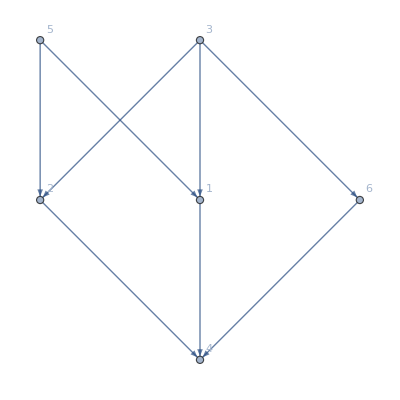

```mathematica
Graph[getDummiesResult["graph with dummies"],VertexLabels->"Name"]
```

```mathematica
le=getDummiesResult["layers with dummies"]
edge=getDummiesResult["graph with dummies"]
```

{{3,5},{2,1,6},{4}}

{2->4,3->2,5->2,3->1,5->1,1->4,3->6,6->4}

```mathematica
amount={};
Do[
step1=Cases[edge,a_->b_/;MemberQ[le[[k]],a]->a->b];
sortedge={};
Do[If[MemberQ[step1,i->j],AppendTo[sortedge,i->j]],{i,le⟦k⟧},{j,le⟦k+1⟧}];(*получаем в правильном порядке ребра*)
AppendTo[amount,Total@Flatten@Table[Position[le[[k+1]],v]-1,{v,sortedge[[All,2]]}]],(*считаем инверсии*){k,Length@le-1}]
```

```mathematica
Total@amount
```

4

## Realisation

```mathematica
ClearAll[InversionAlgorithm]
InversionAlgorithm[G_]:=Module[{amount={},
le=G["layers with dummies"],
edge=G["graph with dummies"],sortedge,step1},
Do[
step1=Cases[edge,a_->b_/;MemberQ[le[[k]],a]->a->b];
sortedge={};
Do[If[MemberQ[step1,i->j],AppendTo[sortedge,i->j]],{i,le⟦k⟧},{j,le⟦k+1⟧}];(*получаем в правильном порядке ребра*)
AppendTo[amount,Total@Flatten@Table[Position[le[[k+1]],v]-1,{v,sortedge[[All,2]]}]],(*считаем инверсии*){k,Length@le-1}];Total@amount
]
```

```mathematica
InversionAlgorithm[getDummiesResult]
```

4

```mathematica
edges={4->8,6->7,8->9,7->10,6->1,1->9,8->10};
layers={{4,6},{7,8,1},{9,10}};
```

```mathematica
test=<|"layers with dummies"->layers,"graph with dummies"->edges|>
```

<|layers with dummies→{{4,6},{7,8,1},{9,10}},graph with dummies→{4->8,6->7,8->9,7->10,6->1,1->9,8->10}|>

```mathematica
InversionAlgorithm[test]
```

5

### Time Test

```mathematica
getDummiesResult=AddDummyVertices[Composition[GetLayering,GetDAG][GetGraph[20]],ApproachOption->"Cut"];
l=getDummiesResult["layers with dummies"];
layers=MapIndexed[v[#2⟦1⟧,#1]&,l,{2}];
rules=MapThread[Rule,{Flatten@l,Flatten@layers}];
edges=getDummiesResult["graph with dummies"];
arcsWithLongConnections=EdgeList@edges/.rules;
arcs=Cases[arcsWithLongConnections,v[e_,a_]->v[b_,c_]->{v[e,a],v[b,c]}];
```

```mathematica
InversionAlgorithm[getDummiesResult]//AbsoluteTiming;
First[%]
getNumberOfCrossings[arcs,layers]//AbsoluteTiming;
First[%]
```

0.0563505

4.13994

Кажется, что мы выигрываем в скорости колоссально.

## Part II

2. Добавить в пакет функцию GetVertexOrder, работающую от одного аргумента: ассоциация с результатом работы функции AddDummyVertices. 
Функция GetVertexOrder ищет порядок вершин на слоях с целью минимизировать количество пересечений ребер многослойного графа по двум алгоритмам: 
2) метод барицентров с заданным числом итераций, по нечетным - итерациям обход графа выполняется сверху вниз (нижний слой сортируется), по четным - снизу вверх (верхний слой сортируется); возвращается лучший результат среди всех итераций [напоминаю, что если  вершина сортируемого слоя не имеет смежных вершин на фиксированном слое, то она сохраняет свою позицию, если вершины имеют одинаковое значение барицентра, то они сохраняют свой относительный порядок полученный на предыдущей итерации; описание близкого к нашему алгоритму метода медиан: A technique for drawing directed graphs - Emden Gansner.pdf, раздел 3. Vertex Ordering Within Ranks, стр. 13-17]. (2 балла)

## Барицентры

```mathematica
getDummiesResult=AddDummyVertices[Composition[GetLayering,GetDAG][GetGraph[10]],ApproachOption->"Cut"];
```

```mathematica
l=getDummiesResult["layers with dummies"];
layers=MapIndexed[v[#2⟦1⟧,#1]&,l,{2}];
rules=MapThread[Rule,{Flatten@l,Flatten@layers}];
edges=getDummiesResult["graph with dummies"];
arcsWithLongConnections=EdgeList@edges/.rules;
arcs=Cases[arcsWithLongConnections,v[e_,a_]->v[b_,c_]->{v[e,a],v[b,c]}];
```

### Пересечение

```mathematica
Clear[isPairOfEdgesCrossing]
isPairOfEdgesCrossing[{edge1_,edge2_},ordering_]:=
	If[
			edge1⟦1⟧ === edge2⟦1⟧ || edge1⟦2⟧ === edge2⟦2⟧,
			0,
			Boole[
				Xor[
					FirstPosition[ordering,edge1⟦1⟧]⟦2⟧ < FirstPosition[ordering,edge2⟦1⟧]⟦2⟧,
					FirstPosition[ordering,edge1⟦2⟧]⟦2⟧ < FirstPosition[ordering,edge2⟦2⟧]⟦2⟧
				]
			]
			
		]
Clear[getNumberOfCrossings]
getNumberOfCrossings[arcs_,order_]:=Total[isPairOfEdgesCrossing[#,order]&/@Subsets[arcs,{2}]]
```

### Решение из файла в классе

```mathematica
Clear[getBarycenterValueExample]
getBarycenterValueExample[vertixID_,order_,adj_]:=
	Module[
		{
			list = SelectFirst[adj,#⟦1⟧==vertixID&,{}]
		},
		If[
			Length[list]==0,
			-1,
			N@Mean[Position[order,#]⟦1,1⟧&/@list⟦2⟧]
		]
	]
```

### Барицентр для двухслойного

```mathematica
Clear[getBarycenterSortForTwoLayers]
getBarycenterSortForTwoLayers[order_, arcs_, adjLists_, first_, second_]:=Module[
{bc, sortV, m,step1,step2,step3},
bc= {#, getBarycenterValueExample[#, order⟦second⟧, adjLists]}&/@ order⟦first⟧;
step1 = GatherBy[DeleteCases[bc, {_,-1}], Last];
step2 = SortBy[step1, #⟦1,2⟧&];
sortV= Flatten[step2⟦All,All,1⟧];
m = (bc/.{{_, a_}/; a≠-1 -> {Missing[]}})⟦All,1⟧;
Do[If[MissingQ[m⟦i⟧],
m⟦i⟧=First[sortV]; 
sortV=Rest[sortV]],
{i,Length[m]}];
ReplacePart[order, first-> m]]
```

#### Применение метода барицентров и медиан

Методы медиан, барицентров и взвешенных медиан являются итерационными. При этом направление обхода графа зависит от четности итерации, если итерация нечетная обход осуществляется от головной вершины к листьям, если четная — от листьев к головной вершине. После проведения каждой итерации определяется текущее число пересечений ребер графа. Если количество пересечений в результате выполнения итерации сокращается, то полученный порядок вершин записывается как «текущий лучший». Следовательно, во время расчета необходимо использовать функцию подсчета количества пересечений на слое. При подсчете пересечений исследуются все пары ребер на данном уровне.

Input: ориентированный граф G=(V,E), и множество начальных перестановок вершин на слоях П_0
Output: набор перестановок П_return;
1  procedure ordering()
2 	П = П_0;
3 	П_return = П;
4 	for i = 0 to Max_iterations do
5 		П = heuristic(П,i);
6		if crossing(П) < crossing(П_return) then
7			П_return = П;
8	end
9	return П_return;
10  end

Следовательно, во время расчета необходимо использовать функцию crossing, которая в качестве исходных данных использует порядок вершин, а на выходе дает число пересечений ребер графа.

### Проверка на четность и нечетность

```mathematica
ClearAll[getVertexOrderBarycenter]
getVertexOrderBarycenter[layers_, arcs_, amountOFiterations_] :=
Module[{order = layers,adjLists,adjListsReverse ,resultOrder,crossers,n=Length[layers],bestresults = {},
step1={#⟦1,2⟧, #⟦All,1⟧} & /@ SortBy[GatherBy[arcs, Last], #⟦1,2⟧ &],
step2={#⟦1,2⟧, #⟦All,1⟧} & /@ SortBy[GatherBy[Reverse /@ arcs, Last], #⟦1,2⟧ &],
pairsOfEdges = Flatten[Subsets[#, {2}] & /@ GatherBy[arcs, #[[1, 1]] &], 1]},
adjLists = Thread[GatherBy[step1 ,#⟦1, 1⟧&]⟦All,1,1,1⟧ -> GatherBy[step1 ,#⟦1, 1⟧ &]];
adjListsReverse =Thread[GatherBy[step2,#⟦1, 1⟧&]⟦All,1,1,1⟧ -> GatherBy[step2 ,#⟦1, 1⟧ &]];
crossers=Total[isPairOfEdgesCrossing[#, order] & /@ pairsOfEdges];
Do[
	If[Mod[iter, 2] != 0,
		Do[order⟦{i, i+1}⟧ = getBarycenterSortForTwoLayers[order⟦{i, i+1}⟧, 
				Select[arcs, #⟦1, 1⟧ == i &], i+1 /. adjLists, 2, 1], {i, n-1}],
		Do[order⟦{i-1, i}⟧ = getBarycenterSortForTwoLayers[order⟦{i-1, i}⟧, 
				Select[arcs, #⟦1, 1⟧ == i-1 &], i-1/.adjListsReverse, 1, 2], {i, n, 2, -1}]];AppendTo[bestresults, {order, crossers}],
{iter,amountOFiterations}
];
resultOrder=MinimalBy[bestresults,Last]⟦1,1⟧
]
```

### Test

```mathematica
results=getVertexOrderBarycenter[layers,arcs,20]
```

{{v[1,8]},{v[2,3],v[2,7],v[2,13],v[2,16],v[2,20],v[2,28],v[2,31]},{v[3,14],v[3,9],v[3,1],v[3,17],v[3,21]},{v[4,15],v[4,25],v[4,10],v[4,11],v[4,18],v[4,22]},{v[5,2],v[5,26],v[5,29],v[5,12],v[5,19],v[5,23]},{v[6,5],v[6,27],v[6,30],v[6,4],v[6,24]},{v[7,6]}}

```mathematica
results[[All,All,2]]
```

{{8},{3,7,13,16,20,28,31},{14,9,1,17,21},{15,25,10,11,18,22},{2,26,29,12,19,23},{5,27,30,4,24},{6}}

```mathematica
getDummiesResult["layers with dummies"]
```

{{8},{3,7,13,16,20,28,31},{9,1,14,17,21},{10,11,15,18,22,25},{2,12,19,23,26,29},{5,4,24,27,30},{6}}

Количество пересечений исходного распределения по слоям и полученного методом Барицентров

```mathematica
getNumberOfCrossings[arcs,layers]
getNumberOfCrossings[arcs,results]
```

365

288

### Test From Package

```mathematica
GetVertexOrder[getDummiesResult]
```

<|acyclic graph→{1->4,2->5,3->9,4->6,7->1,7->9,8->2,8->3,8->4,8->6,9->6},feedback set→{1->7,1->8,2->10,4->2,4->8,6->9,6->10,7->8,9->3,9->8,10->1},graph with dummies→{2->5,3->9,4->6,7->1,7->9,8->3,10->2,2->4,8->7,1->10,1->11,11->12,12->4,8->13,13->14,14->15,15->2,8->16,16->17,17->18,18->19,19->4,8->20,20->21,21->22,22->23,23->24,24->6,9->25,25->26,26->27,27->6,8->28,28->1,10->29,29->30,30->6,8->31,31->9},layers with dummies→{{8},{3,7,13,16,20,28,31},{14,9,1,17,21},{15,25,10,11,18,22},{2,26,29,12,19,23},{5,27,30,4,24},{6}},first dummy→11|>

```mathematica
getNumberOfCrossings[arcs,layers]
getNumberOfCrossings[arcs,MapIndexed[v[#2⟦1⟧,#1]&,GetVertexOrder[getDummiesResult]["layers with dummies"],{2}]]
```

365

288

```mathematica
GetVertexOrder[getDummiesResult,ApproachOption->"barycenter"]
```

<|acyclic graph→{1->4,2->5,3->9,4->6,7->1,7->9,8->2,8->3,8->4,8->6,9->6},feedback set→{1->7,1->8,2->10,4->2,4->8,6->9,6->10,7->8,9->3,9->8,10->1},graph with dummies→{2->5,3->9,4->6,7->1,7->9,8->3,10->2,2->4,8->7,1->10,1->11,11->12,12->4,8->13,13->14,14->15,15->2,8->16,16->17,17->18,18->19,19->4,8->20,20->21,21->22,22->23,23->24,24->6,9->25,25->26,26->27,27->6,8->28,28->1,10->29,29->30,30->6,8->31,31->9},layers with dummies→{{8},{3,7,13,16,20,28,31},{14,9,1,17,21},{15,25,10,11,18,22},{2,26,29,12,19,23},{5,27,30,4,24},{6}},first dummy→11|>

```mathematica
GetVertexOrder[getDummiesResult,ApproachOption->"barycenterD"]
```

GetVertexOrder::option: Option barycenterD is not in list of options. Choose another one from the list: 
barycenter

$Aborted